# Derivation of criteria for best focus

Define the wavefront error and its approximation up to fourth order

```mathematica
abeW[u_,nr_,α_]:=1/nr √(1-( nr u)^2)- α √(1-u^2)
abeW4th[u_,nr_,α_]:=1/nr-α-1/2(nr-α)u^2-1/8(nr^3-α)u^4
abeW6th[u_,nr_,α_]:=1/nr-α-1/2(nr-α)u^2-1/8(nr^3-α)u^4-1/16(nr^5-α) u^6
```

```mathematica
Series[abeW[u,nr,α],{u,0,6}]
```

(1/nr-α)+1/2 (-nr+α) u^2+(-nr^3/8+α/8) u^4+(-nr^5/16+α/16) u^6+O[u]^7

#### Paraxial (second order W rms)

```mathematica
getParaxial[nr_]:=nr
```

#### Fourth order W rms

Note that the nr multiplying the terms is there because the definition is with u running from 0 to 1 (the SA).

```mathematica
Wmean[α_,nr_]=Assuming[{nr>1,α∈Reals},Integrate[nr^2 abeW4th[u,nr,α]u,{u,0,1/nr},{f,0,2π}]/π];
W2mean[α_,nr_] =Assuming[{α∈Reals},Integrate[nr^2(abeW4th[u,nr,α] )^2 u ,{u,0,1/nr},{f,0,2π}]/π];
```

```mathematica
Solve[Assuming[{nr>1,α∈Reals},D[( W2mean[α,nr]-Wmean[α,nr]^2),α]]==0,α]//Simplify
```

{{α→(nr^3 (19+75 nr^2))/(4+30 nr^2+60 nr^4)}}

```mathematica
getW4min[nr_]:=(nr^3 (19+75 nr^2))/(2 (2+15 nr^2+30 nr^4))
```

#### Sixth order W rms

Note that the nr multiplying the terms is there because the definition is with u running from 0 to 1 (the SA).

```mathematica
Wmean[α_,nr_]=Assuming[{nr>1,α∈Reals},Integrate[nr^2 abeW6th[u,nr,α]u,{u,0,1/nr},{f,0,2π}]/π];
W2mean[α_,nr_] =Assuming[{α∈Reals},Integrate[nr^2(abeW6th[u,nr,α] )^2 u ,{u,0,1/nr},{f,0,2π}]/π];
```

```mathematica
Solve[Assuming[{nr>1,α∈Reals},D[( W2mean[α,nr]-Wmean[α,nr]^2),α]]==0,α]//Simplify
```

{{α→(nr^5 (4269+9352 nr^2+36624 nr^4))/(5 (81+336 nr^2+1568 nr^4+2688 nr^6+5376 nr^8))}}

```mathematica
getW6min[nr_]:=(nr^5 (4269+9352 nr^2+36624 nr^4))/(5 (81+336 nr^2+1568 nr^4+2688 nr^6+5376 nr^8))
```

#### Whole W rms

```mathematica
Wmean[α_,nr_]=Assuming[{nr>1,α∈Reals},Integrate[nr^2 abeW[u,nr,α]u,{u,0,1/nr},{f,0,2π}]/π];
W2mean[α_,nr_] =Assuming[{α∈Reals},Integrate[nr^2(abeW[u,nr,α])^2 u ,{u,0,1/nr},{f,0,2π}]/π];
```

```mathematica
Solve[Assuming[{nr>1,α∈Reals},D[( W2mean[α,nr]-Wmean[α,nr]^2),α]]==0,α]//Simplify
```

{{α→ConditionalExpression[(-9 nr+7 nr^3+16 √(-1+nr^2)-16 nr^2 √(-1+nr^2)+9 (-1+nr^2)^2 ArcCoth[nr])/(2+12 nr^2-48 nr^4+32 nr^6+32 nr^3 √(-1+nr^2)-32 nr^5 √(-1+nr^2)), nr>1]}}

```mathematica
getWmin[nr_]:=(-9 nr+7 nr^3+16 √(-1+nr^2)-16 nr^2 √(-1+nr^2)+9 (-1+nr^2)^2 ArcCoth[nr])/(2+12 nr^2-48 nr^4+32 nr^6+32 nr^3 √(-1+nr^2)-32 nr^5 √(-1+nr^2))
```

#### Min spot size 4th order

```mathematica
ϵx[u_,ϕ_,α_,nr_]=D[abeW4th[u,nr,α]/.u->(√(ux^2+uy^2)),ux]/.ux->u Cos[ϕ]/.uy->u Sin[ϕ]//Simplify;
ϵ2mean[α_,nr_] = Assuming[{nr>1,α∈Reals},Integrate[nr^2 (ϵx [u,f,α,nr])^2 u,{u,0,1/nr},{f,0,2π}]/π];
```

```mathematica
Solve[Assuming[{nr>1,α∈Reals},D[ϵ2mean[α,nr],α]]==0,α]//Simplify
```

{{α→(nr^3 (11+32 nr^2))/(3+16 nr^2+24 nr^4)}}

```mathematica
getϵ4min[nr_]:=(nr^3 (11+32 nr^2))/(3+16 nr^2+24 nr^4)
```

#### Min spot size 6th

```mathematica
ϵx[u_,ϕ_,α_,nr_]=D[abeW6th[u,nr,α]/.u->(√(ux^2+uy^2)),ux]/.ux->u Cos[ϕ]/.uy->u Sin[ϕ]//Simplify;
ϵ2mean[α_,nr_] = Assuming[{nr>1,α∈Reals},Integrate[nr^2 (ϵx [u,f,α,nr])^2 u,{u,0,1/nr},{f,0,2π}]/π];
```

```mathematica
Solve[Assuming[{nr>1,α∈Reals},D[ϵ2mean[α,nr],α]]==0,α]//Simplify
```

{{α→(nr^5 (297+512 nr^2+1460 nr^4))/(45+144 nr^2+480 nr^4+640 nr^6+960 nr^8)}}

```mathematica
getϵ6min[nr_]:=(nr^5 (297+512 nr^2+1460 nr^4))/(45+144 nr^2+480 nr^4+640 nr^6+960 nr^8)
```

#### Confusion

```mathematica
getLeastConfusion[smax_,nr_]:=-(x/.NSolve[-((smax/(√(1-smax^2))+(smax x)/(nr √(1-smax^2/nr^2)))√(1-(1/nr)^2))^(2/3)+(-x/nr)^(2/3)==1,x][[1]])
```

θ is the angle of the ray emerging from the source, x the position with the zero at the interface

```mathematica
a[θ_,ni_,nf_]:=(ni Sin[θ]/nf)/(√(1-(ni Sin[θ]/nf)^2))
b[θ_,ni_,nf_,d_]:=d Tan[θ]
r[ϕ_,θ_,ni_,nf_,d_]:=b[θ,ni,nf,d]/(Sin[ϕ]-a[θ,ni,nf]Cos[ϕ])
y[x_,θ_,ni_,nf_,d_]:=a[θ,ni,nf]x+b[θ,ni,nf,d]
```

### Comparisson

```mathematica
With[{nr = 1.515/1.33},
{getParaxial[nr],getW4min[nr],getW6min[nr],getWmin[nr],getϵ4min[nr],getϵ6min[nr],getLeastConfusion[1/nr,nr]}]
```

{1.1391,1.19434,1.23384,1.39502,1.20977,1.27106,1.41167}

```mathematica
plotRaysInterface[ni_,nf_,na_]:=With[{dcs=50,numθ=25,α=1.5},
Block[{nr,pry=0.5*dcs,θimax,θilist,θflist,αpar,αϵlist,prxm,prxp,αlc,αWlist},
nr = nf/ni;
prxm=-2.5dcs(*(.1+α)nf dcs/ni*);
prxp=0.1nf dcs/ni;
θimax=ArcSin[na/nf];
θilist=Join[Table[θ,{θ,-θimax,-θimax/numθ,θimax/numθ}],Table[θ,{θ,θimax/numθ,θimax,θimax/numθ}]];
θflist=ArcSin[ni/nf Sin[#]]&/@θilist;
αlc =getLeastConfusion[1/nr,nr];
αpar=getParaxial[nr];
αWlist = {getW4min[nr],getW6min[nr],getWmin[nr]};
αϵlist = {getϵ4min[nr],getϵ6min[nr]};
Show[{
Graphics[{
{{Thick,Line[{{0,-pry},{0,pry}}]},
Dotted,AbsoluteThickness[1.2],Line[{{-dcs,-pry},{-dcs,pry}}],
DotDashed,Line[{{-αpar dcs,-pry},{-αpar dcs,pry}}],(*Line[{{-αderW dcs,-pry},{-αderW dcs,pry}}],*)
Dashed,
(*LEast confusion*)
Magenta,Line[{{-αlc dcs,-pry},{-αlc dcs,pry}}],
(*Wavefront focuses*)
Table[{Darker[RGBColor[0.,0.69,1.],(i-1)/4],Line[{{-αWlist[[i]]dcs,-pry},{-αWlist[[i]] dcs,pry}}]},{i,1,3}],
(*Spot size*)
Table[{Darker[RGBColor[0.9,0.54,0.],(i-1)/4],Line[{{-αϵlist[[i]]dcs,-pry},{-αϵlist[[i]] dcs,pry}}]},{i,1,2}]},
(*Source rays*)
{Blue,Thin,Line[{{-dcs,0},{0,0}}],Line[{{-dcs,0},{0,dcs Tan[#]}}]&/@θilist},
(*Refracted rays*)
{Hue[0.88,1.,0.65], Thin, Line[{{prxm,0},{prxp,0}}],Line[{{prxm,y[prxm,#,ni,nf,dcs]},{prxp,y[prxp,#,ni,nf,dcs]}}]&/@θilist}}
],
(*Caustic*)
ParametricPlot[{(-dcs nf)/ni Cosh[θ]^3,(dcs nf)/(√(nf^2-ni^2))Sinh[θ]^3},{θ,-π/2,π/2},PlotStyle->{Red,Thick}]}
,PlotRange->{{prxm,prxp},{-pry,pry}}]
]]
```

```mathematica
savePath = FileNameJoin[{NotebookDirectory[],"figures","best_focus"}]
```

/Users/rodrigo/Documents/Research/CHIDO/pyPSFstack/figures/best_focus

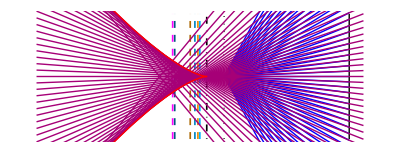

/Users/rodrigo/Documents/Research/CHIDO/pyPSFstack/figures/best_focus/IntWaterOil.pdf

```mathematica
plotRaysInterface[1.33,1.515,1.33]
Export[FileNameJoin[{savePath ,"IntWaterOil.pdf"}],%]
```

```mathematica
With[{nr = 1.515/1.33},
{getParaxial[nr],getW4min[nr],getW6min[nr],getWmin[nr],getϵ4min[nr],getϵ6min[nr],getLeastConfusion[1/nr,nr]}]
```

{1.1391,1.19434,1.23384,1.39502,1.20977,1.27106,1.41167}

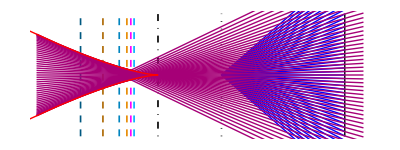

/Users/rodrigo/Documents/Research/CHIDO/pyPSFstack/figures/best_focus/IntAirOil.pdf

```mathematica
plotRaysInterface[1.,1.515,1.]
Export[FileNameJoin[{savePath ,"IntAirOil.pdf"}],%]
```

```mathematica
With[{nr = 1.515},
{getParaxial[nr],getW4min[nr],getW6min[nr],getWmin[nr],getϵ4min[nr],getϵ6min[nr],getLeastConfusion[1/nr,nr]}]
```

{1.515,1.70888,1.82928,2.14297,1.76728,1.96151,1.73516}